# Practical - 6

HARIOM (20201022)

Show that the image of the right half plane A = { 
 z: Re(z) ≥ 1/2} under the mapping w = f(z) = 1/z is the closed disk
 {w: |w - 1| ⩽ 1}.

```mathematica
Clear[z]
```

The right half plane Re(z)≥1/2 is given by the figure

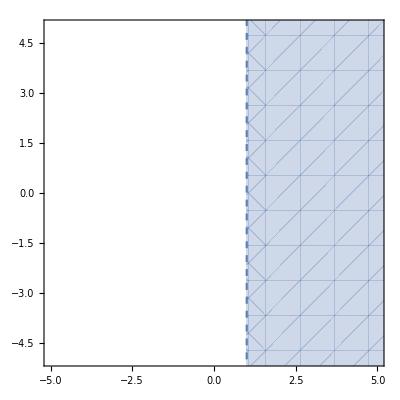

The image of the right half plane Re(z)≥1/2 under the function f(z)= 1/z is given by the figure

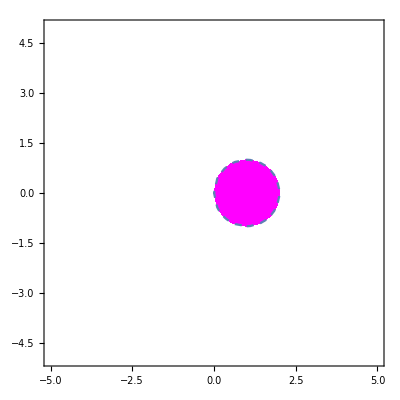

```mathematica
Print["The right half plane Re(z)≥1/2 is given by the figure"];
RegionPlot[Re[x+I*y]≥1,{x,-10,10},{y,-10,10},BoundaryStyle->Dashed,PlotRange->5,Axes->True]
f[z_]:=1/z;
w=u+I*v;
root:=z/.ComplexExpand[Solve[f[z]==w,z]]
Print["The image of the right half plane Re(z)≥ 1/2 under the function f(z)= ",f[z]," is given by the figure"];
RegionPlot[Re[root[[1]]]>1/2,{u,-10,10},{v,-10,10},PlotStyle->Magenta,BoundaryStyle->Dashed,PlotRange->5,Axes->True]
```